Failure Repair Dynamics Study

Estrada-Galinanes Veronica

Espigule-Pons Jofre

University of Neuchatel

Decay in a long-term storage system with cumulative failures

Decay in a long-term storage system with cumulative failures

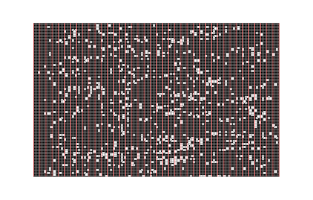
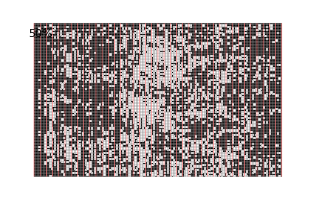

Abstract

GOAL OF THE PROJECT: Understand the behavior of entanglement codes using simple computational models like cellular automata.

SUMMARY OF WORK: Entanglement codes are a technique to create redundant information in the system. They tangling new data blocks with old ones, building entangled data chains that are woven into a growing mesh of interdependent content.  

This project is about the development of a research framework to study failure repair dynamics on storage systems. The program allows playing with code settings and distinct failure assumptions. 

The figures showed above illustrate the dynamics of a storage system under constant failure injection. Each cell represents a storage unit. The color black indicates that the cell is available. The grid is subdivided in columns of 4 cells wide, indicated with pink lines. The cell at the left of the line represents data while the other cells represent redundant information. At each step a certain percentage of failures are injected to the available cells, coloring the cell with “white”, while the system keeps trying to recover the missing cells.

RESULTS AND FUTURE  WORK: This technique seems a good way to study entanglement codes as well as other codes use in storage systems. I plan to continue this research direction to compare entanglement with other codes. In addition, I would like to improve the failure model and include repair constrains.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Failure Repair Dynamics of Storage Systems

Failure Repair Dynamics of Storage Systems

Simple Entanglement Codes

-Graphics-

Three Failure patterns cause data loss

Complex Entanglement Codes

Enumerating all failure patterns is difficult

REPAIRS - CELLULAR AUTOMATA

```mathematica
-Graphics-}
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Visualization 1: Animation that shows the repair cycles of entanglement codes. It is easy to observe that repairs can be done mostly in parallel and after the first 1-2 rounds most of the missing elements are recovered even in the process of a large amount of failures. In this case, failures only occur at the beginning.

Visualization 2: Visualization of the dynamics of the repair process in a system that failures are injected at each step while the system keeps doing repairs to recover data and survive.

Code

https://github.com/koleosfuscus/WolframSS17/blob/master/EntanglementVisualizations.nb

Written Content / Lesson Plans

Not applicable to my track.

Conclusions in Detail

Initially, I tried to adapt the cellular automata Mathematica implementation to simulate alpha entanglement code behavior but it didn’t work. Given the short time for this project, I opted for implementing the automaton rules from scratch. I also tried various visualizations mentioned in the book “A New Kind of Science” such as the causal networks described in page 492. I found that this visualization is not convenient for entanglement codes because it creates a more complex graph. Finally, I create images and animations to show the encoding and repair behavior.

Finding a good a visualization is not an easy task. I explore many approaches until I took the current direction. Probably, the NKS book has other interesting visualization approaches to try but I didn’t have time to read it completely. 

Rapid prototyping is not a good approach to code entanglement codes as it seems that you can achieve results very fast but later you may encounter plenty of problems and bugs. In spite of the coding simple rules, there are plenty of space to make mistakes. Instead, I encourage carefully thinking of what you are trying to achieve before start touching code and make the code “dirty”. The code written for this project is not curated. It is the result of exploring many different visualizations and its evolution to provide new functionality. Moreover, I do not have experience with Mathematica and functional programming. That means that during the last three weeks the code somehow follows my language learning curve. In spite of this self-criticism, I think the code is pretty decent to the resources provided and how the project goals have evolved during these three weeks.    

The selected visualizations are promising. The study of failure patterns in entanglement codes has not being easy task due to the exponential combination of patterns that can appear. However, I can exploit the current code to study the code’s behavior. I’m interested in further developing the ideas behind this project.

All Visualizations

The first picture shows the state of the system after 50% of the data (circles) and encoded data (diamonds) became unavailable. Red colored units indicate failure. Repairs are performed simultaneously assuming the system has enough resources. The system is recovered after 5 repair cycles. Disclaimer: Only the repair algorithm is implemented. The encoding algorithm is not yet finished. Therefore the colored values for diamonds do not carry any meaning.

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

Data Sources Links/References

This project does not use any external data source.

Future Directions

Some ideas that I’d like to explore:

Differentiate between content and storage locations. At the moment, the number of failure domains is equivalent to the number of cells. It is interesting to figure out what happen if some cells are stored in the same failure domain.

Comparison with other codes.

Background Info Links/References

Wolfram, Stephen. A new kind of science. Vol. 5. Champaign: Wolfram media, 2002.
Estrada-Galinanes, Vero, Jehan-François Pâris, and Pascal Felber. “Simple data entanglement layouts with high reliability.” Performance Computing and Communications Conference (IPCCC), 2016 IEEE 35th International. IEEE, 2016.
Galinanes, Veronica Estrada, and Pascal Felber. “Helical entanglement codes: An efficient approach for designing robust distributed storage systems.” Symposium on Self-Stabilizing Systems. Springer, Cham, 2013.
Estrada-Galinanes, Vero. “A research playground for examining erasure codes.” Proceedings of the 10th ACM International Systems and Storage Conference. ACM, 2017.

Keywords

Provide keywords as items

entanglement codes

system reliability

archival storage

survival systems

failure repair

erasure codes

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```